```mathematica
(* probelm one loose ends*) (*please run them cell by cell to have manipulate fuction work proberly*)
```

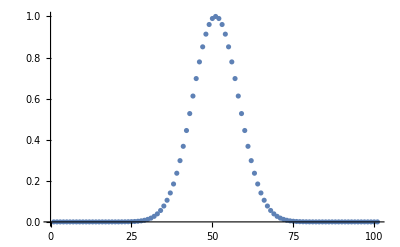

```mathematica
k=100;dx=.01;c=30;dt=dx/c;r=1;x=Range[0,1,dx];tf=1000;t=Range[0,tf dt,dt];lx=Length@x;lt=Length@t;y=ConstantArray[0,{lt,lx}];y[[1]]= Exp[- k (x-.5)^2];y[[2]]=y[[1]];ListPlot[y[[1]]]
Do[
Do[y[[n,i]]=2(1-r^2) y[[n-1,i]]-y[[n-2,i]]+r^2(y[[n-1,i+1]]+y[[n-1,i-1]]),{i,2,lx-1}];y[[n,lx]]=y[[n,lx-1]];y[[n,1]]=y[[n,2]]

,{n,3,lt}];
Manipulate[ListPlot[y[[i]],PlotRange->{{0,100},{-1,1}},Joined->True],{i,1,lt,1}]
```

```mathematica
(*problem 6 checking linearity of EOM*)
```

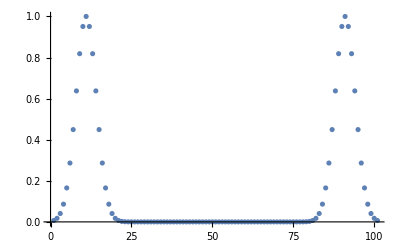

```mathematica
k=500;dx=.01;c=30;dt=dx/c;r=1;x=Range[0,1,dx];tf=1000;t=Range[0,tf dt,dt];lx=Length@x;lt=Length@t;y=ConstantArray[0,{lt,lx}];y[[1]]= Exp[- k (x-.9)^2]+Exp[- k (x-.1)^2];y[[2]]=y[[1]];ListPlot[y[[1]]]
Do[
Do[y[[n,i]]=2(1-r^2) y[[n-1,i]]-y[[n-2,i]]+r^2(y[[n-1,i+1]]+y[[n-1,i-1]]),{i,2,lx-1}];

,{n,3,lt}];Manipulate[ListPlot[y[[i]],PlotRange->{{0,100},{-1,1}},Joined->True],{i,1,lt,1}]
```

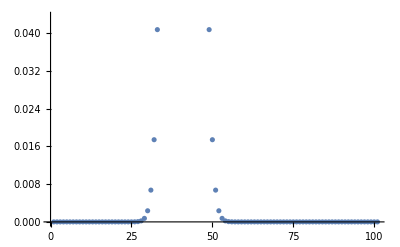

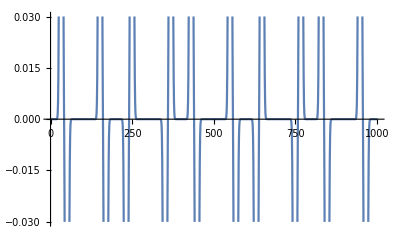

```mathematica
k=500;dx=.01;c=10;dt=dx/c;r=1;x=Range[0,1,dx];tf=1000;t=Range[0,tf dt,dt];lx=Length@x;lt=Length@t;y=ConstantArray[0,{lt,lx}];y[[1]]= Exp[- k (x-.4)^2];y[[2]]=y[[1]];ListPlot[y[[1]]]
Do[
Do[y[[n,i]]=2(1-r^2) y[[n-1,i]]-y[[n-2,i]]+r^2(y[[n-1,i+1]]+y[[n-1,i-1]]),{i,2,lx-1}];y[[n,lx]]=y[[n,lx-1]];

,{n,3,lt}]
Manipulate[ListPlot[y[[i]],PlotRange->{{0,100},{-1,1}},Joined->True],{i,1,lt,1}]
ListPlot[y[[;;,10]],Joined->True]
```

```mathematica
f=c/4 (* calcualte the fundamental harmonic*)
```

5/2

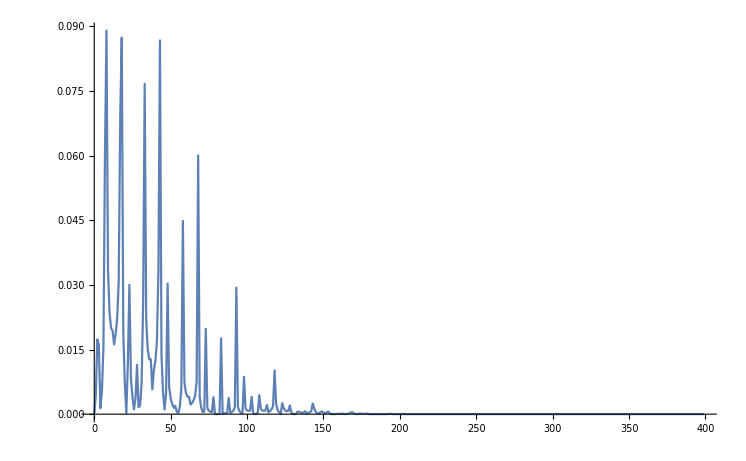

```mathematica
dftdata = Abs[Fourier[y[[;;,20]],FourierParameters->{1,-1}]];
fData =  Table[{(i-1)/t[[-1]],2dftdata[[i]]/Length[t]},{i,Length[t]}];
ListPlot[fData[[1;;400]], PlotRange->All, Joined->True]
```

```mathematica
peaks = FindPeaks[dftdata];
peaks[[1]][[1]]
```

3

```mathematica
(* first frequency appears at f= 3 which is near 2.5 the calcualted value*)
```

```mathematica
MatrixForm[peaks[[1;;7]]]
```

(3 | 8.67989
9 | 44.5396
19 | 43.7251
24 | 15.0141
29 | 5.72769
34 | 38.3654
44 | 43.42)

```mathematica
(* f=n v/4 where n is odd as we expect the first column shows the freqeuncies at the peaks which is nearly the odd multible of the fundamental*)
```

```mathematica
(*last part done in two way*)
```

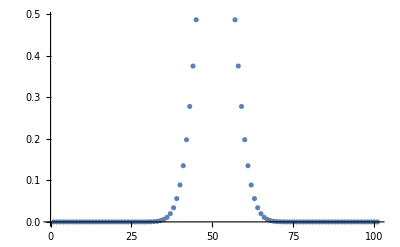

```mathematica
k=200;dx=.01;c=10;dt=dx/(4 c);r=c dt/dx;x=Range[0,1,dx];tf=1000;t=Range[0,tf dt,dt];lx=Length@x;lt=Length@t;y=ConstantArray[0,{lt,lx}];M=1/dx; ϵ=10^-5;y[[1]]= Exp[- k (x-.5)^2];y[[2]]=y[[1]];

y[[1,lx-1]]=0;y[[1,lx]]=-y[[1,lx-2]];
y[[2,lx-1]]=0;y[[2,lx]]=- y[[2,lx-2]];
y[[1,2]]=0;y[[1,1]]=- y[[1,3]];
y[[2,2]]=0;y[[2,1]]=- y[[2,3]];ListPlot[y[[1]]]
Do[
Do[y[[n,i]]=(2−2 r^2−6ϵ r^2 M^2) y[[n-1,i]]-y[[n-2,i]]+ r^2(1+4ϵ M^2)(y[[n-1,i+1]]+y[[n-1,i-1]])− ϵ r^2 M^2(y[[n-1,i+2]]+y[[n-1,i-2]]),{i,3,lx-2}];

y[[n,2]]=0;  y[[n,1]]=- y[[n,3]];y[[n,lx-1]]=0; y[[n,lx]]=- y[[n,lx-2]];
,{n,3,lt}]
```

```mathematica
Manipulate[ListPlot[y[[i]],PlotRange->{{0,100},{-1,1}},Joined->True],{i,1,lt,1}]
```

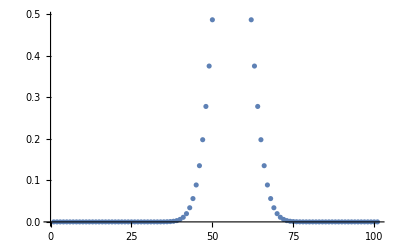

```mathematica
k=200;dx=.01;c=300;dt=dx/(4 c);rr=c dt/dx;x=Range[0,1,dx];tf=1000;t=Range[0,tf dt,dt];lx=Length@x;lt=Length@t;ya=ConstantArray[0,{lt,lx}];M=1/dx; ϵ=10^-5;ya[[1]]= Exp[- k (x-.55)^2];ya[[2]]=ya[[1]];

ListPlot[ya[[1]]]
Do[
Do[ya[[n,i]]=(2-2 rr^2-6 ϵ rr^2 M^2) ya[[n-1,i]]-ya[[n-2,i]]+rr^2 (1+4 ϵ M^2) (ya[[n-1,i+1]]+ya[[n-1,i-1]])-ϵ rr^2 M^2*If[i==lx-1,-ya[[n-1,lx-1]],ya[[n-1,i+2]]]-ϵ (rr^2) (M^2)*If[i==2,-ya[[n-1,2]],ya[[n-1,i-2]]],{i,2,lx-1}]


,{n,3,lt}]
```

```mathematica
Manipulate[ListPlot[ya[[i]],PlotRange->{{0,100},{-1,1}},Joined->True],{i,1,lt,1}]
```

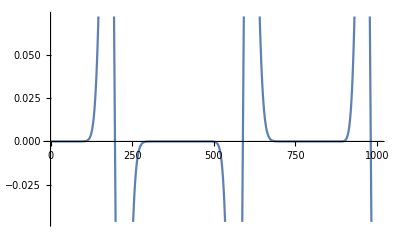

```mathematica
ListPlot[y[[;;,-5]],Joined->True]
```

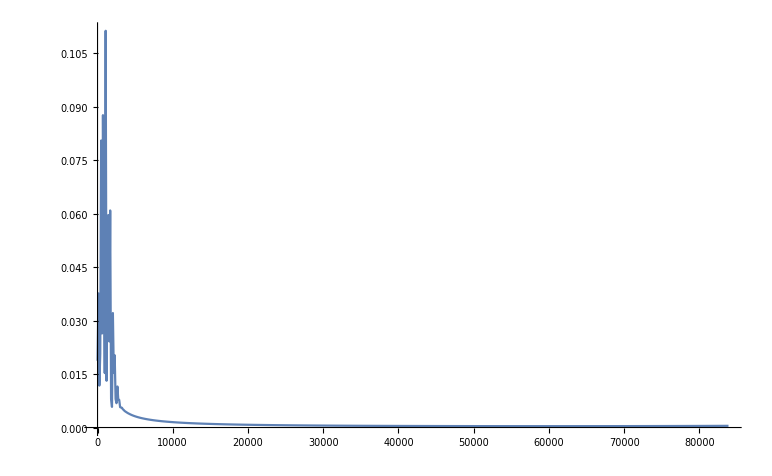

```mathematica
dftdata = Abs[Fourier[y[[;;,6]],FourierParameters->{1,-1}]];
fData =  Table[{(i-1)/t[[-1]],2dftdata[[i]]/Length[t]},{i,Length[t]}];
ListPlot[fData[[1;;700]], PlotRange->All, Joined->True]
```

```mathematica
(* high freq don not apear why|*)
```